```mathematica
SetDirectory[NotebookDirectory[]];
pred=RGBColor[1,0,0,0.65];
pyellow=RGBColor[1,1,0,0.65];
pblue=RGBColor[173/255,216/255,230/255,0.65];
pgreen=RGBColor[1,0,1,0.65];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#<-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#<0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#<Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#<Pi}}]&;
phase[l:{_?NumericQ..}]:=Module[{args=l},(args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0])];
rasterizeBackground[g_,res_:100]:=Module[{raster},raster=Rasterize[Show[g,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,PlotRangeClipping->False,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],If[Length[ImageSize/.Options[g]]==2,AspectRatio->(ImageSize/.Options[g])[[2]]/(ImageSize/.Options[g])[[1]],AspectRatio->(AspectRatio/.Options[g])]],ImageResolution->res];
Graphics[{Raster[raster[[1,1]],Transpose[PlotRange/.Quiet[AbsoluteOptions[g]]],raster[[1,3]]]},#]&@(Options[g]/.(Epilog->epi_):>Epilog->{})]
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/oscillators/uncorrelated

{2,1000.000000,0.010000,10.000000,0.950000}

{100000,2}

{1.20095,1.14053}

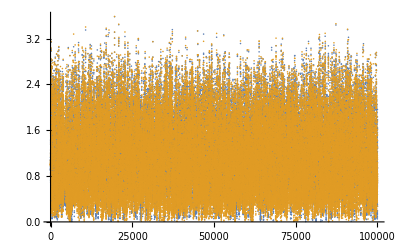

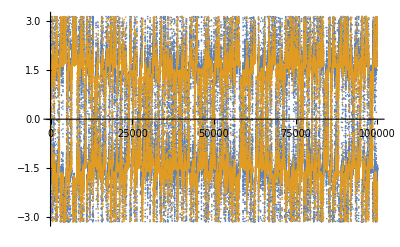

```mathematica
filebase="data/test2";
file="data/test";
strlst=ReadList[file<>".out",String];
lst=StringSplit[First[strlst]]
n=ToExpression[lst[[1]]];
t1=Internal`StringToDouble[lst[[2]]];
dt=Internal`StringToDouble[lst[[3]]];
σ=Internal`StringToDouble[lst[[4]]];
K=Internal`StringToDouble[lst[[5]]];
Nt=Floor[t1/dt];
file=OpenRead[filebase<>".dat",BinaryFormat->True];
dat=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"],2],2];
Close[file];
Dimensions[dat]
Mean[Abs[dat[[1;;-1]]]]
ListPlot[Transpose[Abs[dat[[1;;-1]]]]]
ListPlot[Transpose[Arg[dat[[1;;-1]]]]]
```

```mathematica
imgSize={400,300};
imgPadding={{75,50},{50,50}};
cases=Sort[Import["data/noise/uncorrelatedadd1meanphase.dat"][[All,6]]];
uncorrelatedadd1=Import["data/noise/uncorrelatedadd1meanphase.dat"];
correlatedadd1=Import["data/noise/correlatedadd1meanphase.dat"];
uncorrelatedadd2=Import["data/noise/uncorrelatedadd2meanphase.dat"];
correlatedadd2=Import["data/noise/correlatedadd2meanphase.dat"];
f[x_]:=Transpose[{cases,Mean[Cases[x,u_/;u[[6]]==#][[All,19]]]&/@cases}];
f2[x_]:=Transpose[{cases,Mean[Cases[x,u_/;u[[6]]==#][[All,18]]]&/@cases}];
correlatedmult1=Import["data/noise2/correlatedmult1meanphase.dat"];
uncorrelatedmult1=Import["data/noise2/uncorrelatedmult1meanphase.dat"];
cases2=Sort[Import["data/noise/uncorrelatedmult1meanphase.dat"][[All,6]]];
```

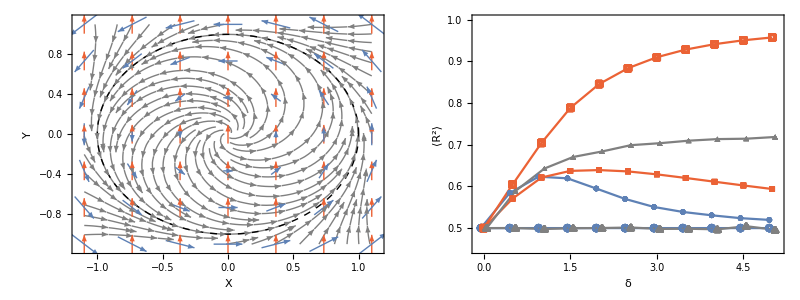

```mathematica
imgSize2={400,400};
imgPadding2={{95,5},{75,10}};
p5=ListPlot[{{#[[1]]-0.05,#[[2]]}&/@f[uncorrelatedadd1],{#[[1]]-0.05,#[[2]]}&/@f[correlatedadd1],f[uncorrelatedadd2],f[correlatedadd2],{#[[1]]+0.05,#[[2]]}&/@f2[uncorrelatedmult1],{#[[1]]+0.05,#[[2]]}&/@f2[correlatedmult1]},Axes->False,Frame->True,FrameLabel->{δ,AngleBracket[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,1}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[1]],Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[1]],AbsoluteThickness[2],Circle[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[4]],Rectangle[]}],0.05},{Graphics[{EdgeForm[Directive[ColorData[97,"ColorList"][[4]],AbsoluteThickness[2]]],FaceForm[None],Rectangle[]}],0.05},{Graphics[{Gray,Triangle[{{0,0},{1,0},{1/2,3^(1/2)/2}}]}],0.05},{Graphics[{EdgeForm[Directive[Gray,AbsoluteThickness[2]]],FaceForm[None],Triangle[{{0,0},{1,0},{1/2,3^(1/2)/2}}]}],0.05}},PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[Gray],Directive[Gray]},AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True];
p1=StreamPlot[{x-y-(x^2+y^2)*x,y+x-(x^2+y^2)*y},{x,-1.1,1.1},{y,-1.1,1.1},LabelStyle->Directive[24,Black], FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{Y,None},{X,None}},ImageSize->imgSize2,ImagePadding->imgPadding2,StreamStyle->Gray];
p2=VectorPlot[{-y,x},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.1,VectorStyle->{Thick,ColorData[97,"ColorList"][[1]]}];
p3=VectorPlot[{0,1},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.06,VectorStyle->{Thick,ColorData[97,"ColorList"][[4]]}];
p4=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Directive[Black,Thick,Dashed]];
p0=Show[p1,p3,p2,p4,ImageSize->imgSize2,ImagePadding->imgPadding2];
p=Grid[{{p0,p5}}]
```

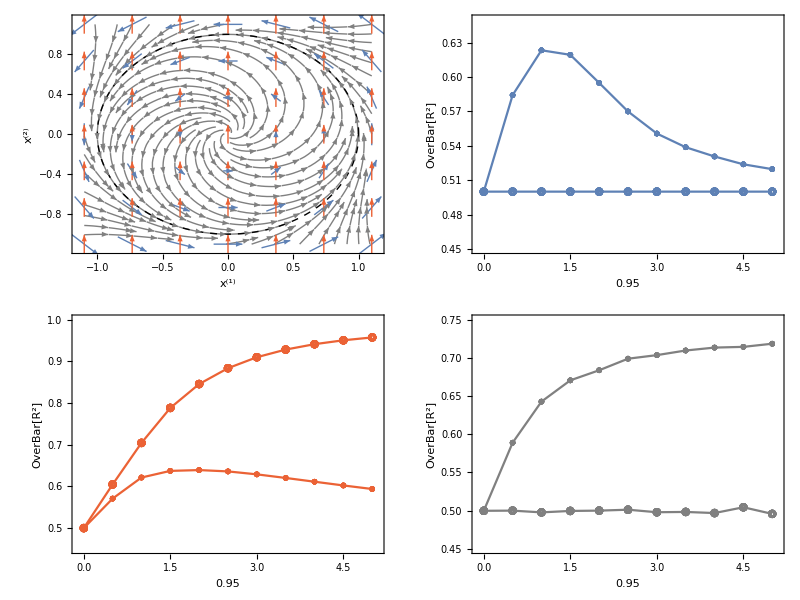

```mathematica
p1=StreamPlot[{x-y-(x^2+y^2)*x,y+x-(x^2+y^2)*y},{x,-1.1,1.1},{y,-1.1,1.1},LabelStyle->Directive[24,Black], FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{Superscript[x,"(2)"],None},{Superscript[x,"(1)"],None}},ImageSize->imgSize2,ImagePadding->imgPadding2,StreamStyle->Gray];
p2=VectorPlot[{-y,x},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.1,VectorStyle->{Thick,ColorData[97,"ColorList"][[1]]}];
p3=VectorPlot[{0,1},{x,-1.1,1.1},{y,-1.1,1.1},VectorPoints->Flatten[Table[{i,j},{i,-1.1,1.1,2.2/6},{j,-1.1,1.1,2.2/6}],1],VectorScale->0.06,VectorStyle->{Thick,ColorData[97,"ColorList"][[4]]}];
p4=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Directive[Black,Thick,Dashed]];
p0=Show[p1,p2,p3,p4,ImageSize->imgSize2,ImagePadding->imgPadding2];

p=Grid[{{p0,ListPlot[{{#[[1]],#[[2]]}&/@f[uncorrelatedadd1],{#[[1]],#[[2]]}&/@f[correlatedadd1]},Axes->False,Frame->True,FrameLabel->{K,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,0.65}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[1]],Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[1]],AbsoluteThickness[2],Circle[]}],0.05}},PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True]},{ListPlot[{f[uncorrelatedadd2],f[correlatedadd2]},Axes->False,Frame->True,FrameLabel->{K,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,1}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[4]],Disk[]}],0.05},{Graphics[{ColorData[97,"ColorList"][[4]],AbsoluteThickness[2],Circle[]}],0.05}},PlotStyle->Directive[ColorData[97,"ColorList"][[4]]],AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True],ListPlot[{{#[[1]],#[[2]]}&/@f2[uncorrelatedmult1],{#[[1]],#[[2]]}&/@f2[correlatedmult1]},Axes->False,Frame->True,FrameLabel->{K,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,0.75}},PlotMarkers->{{Graphics[{Gray,Disk[]}],0.05},{Graphics[{Gray,AbsoluteThickness[2],Circle[]}],0.05}},PlotStyle->Directive[Gray],AspectRatio->1,ImageSize->imgSize2,
ImagePadding->imgPadding2,Joined->True]}}]
```

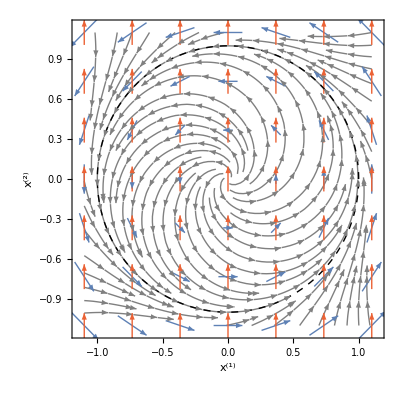
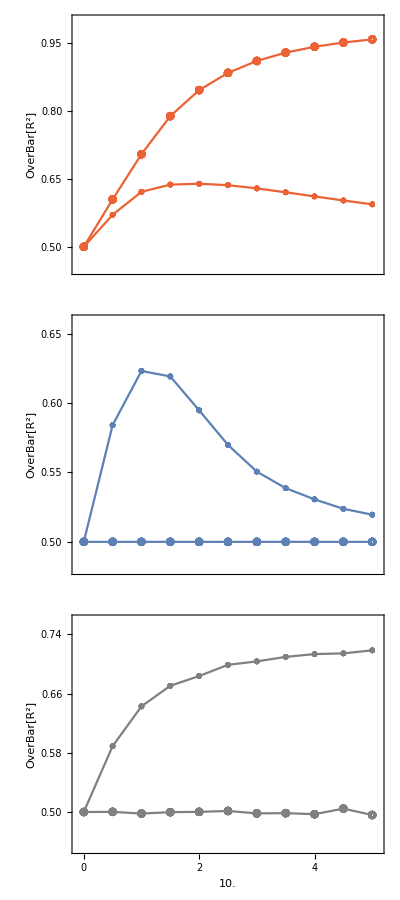
-Graphics- | -Graphics-

plots/fig4.pdf

```mathematica
p=Grid[{{p0,Grid[{{ListPlot[{f[uncorrelatedadd2],f[correlatedadd2]},Axes->False,Frame->True,FrameLabel->{None,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,1.0}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[4]],Disk[]}],0.15},{Graphics[{ColorData[97,"ColorList"][[4]],AbsoluteThickness[2],Circle[]}],0.15}},FrameTicks->{{Table[{r,PaddedForm[r,{3,2}]},{r,0.5,0.96,0.15}],Table[{r,""},{r,0.5,0.96,0.15}]},{Table[{i,""},{i,0,5}],Table[{i,""},{i,0,5}]}},ImagePadding->{{100,10},{10,10}},PlotStyle->Directive[ColorData[97,"ColorList"][[4]]],AspectRatio->1/3,ImageSize->375,Joined->True]},{ListPlot[{{#[[1]],#[[2]]}&/@f[uncorrelatedadd1],{#[[1]],#[[2]]}&/@f[correlatedadd1]},Axes->False,Frame->True,FrameLabel->{None,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.48,0.66}},PlotMarkers->{{Graphics[{ColorData[97,"ColorList"][[1]],Disk[]}],0.15},{Graphics[{ColorData[97,"ColorList"][[1]],AbsoluteThickness[2],Circle[]}],0.15}},FrameTicks->{{Table[{r,PaddedForm[r,{3,2}]},{r,0.5,0.65,0.05}],Table[{r,""},{r,0.5,0.65,0.05}]},{Table[{i,""},{i,0,5}],Table[{i,""},{i,0,5}]}},ImagePadding->{{100,10},{10,10}},PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],AspectRatio->1/3,ImageSize->375,Joined->True]},{ListPlot[{{#[[1]],#[[2]]}&/@f2[uncorrelatedmult1],{#[[1]],#[[2]]}&/@f2[correlatedmult1]},Axes->False,Frame->True,FrameLabel->{σ,OverBar[R^2]},LabelStyle->Directive[24,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{-0.1,5.1},{0.45,0.76}},PlotMarkers->{{Graphics[{Gray,Disk[]}],0.15},{Graphics[{Gray,AbsoluteThickness[2],Circle[]}],0.15}},FrameTicks->{{Table[{r,PaddedForm[r,{3,2}]},{r,0.5,0.8,0.08}],Table[{r,""},{r,0.5,0.8,0.08}]},{Table[{i,i},{i,0,5}],Table[{i,""},{i,0,5}]}},ImagePadding->{{100,10},{100,10}},PlotStyle->Directive[Gray],AspectRatio->1/3,ImageSize->375,Joined->True]}}]}}]
Export["plots/fig4.pdf",p]
```

```mathematica
Z={D[ArcTan[y,x],x],D[ArcTan[y,x],y]}
h=Simplify[{Re[#],Im[#]}&@Expand[1/2*((x+I*y)*(u-I*v)-(u+I*v)*(x-I*y))*(x+I*y)],Element[x,Reals]&&Element[y,Reals]&&Element[u,Reals]&&Element[v,Reals]]
g1={y,-x}
g2={0,1}
```

{y/(x^2+y^2),-x/(x^2+y^2)}

{y (v x-u y),x (-v x+u y)}

{y,-x}

{0,1}

```mathematica
Integrate[Z.h/(2*Pi)/.{x->Cos[θ1+ϕ],y->Sin[θ1+ϕ],u->Cos[θ2+ϕ],v->Sin[θ2+ϕ]},{ϕ,0,Pi}]
FullSimplify[Z.g1/.{x->Cos[θ1],y->Sin[θ1]}]
FullSimplify[Z.g2/.{x->Cos[θ1],y->Sin[θ1]}]
```

-1/2 Sin[θ1-θ2]

1

-Cos[θ1]

```mathematica
z[n_,t_]:=r[n,t]*Exp[I*θ[n,t]]
zc[n_,t_]:=r[n,t]*Exp[-I*θ[n,t]]
Simplify[zc[1,t]*ζ[1,t]*((1+I*α[1])*z[1,t]-z[1,t]*zc[1,t]*z[1,t]-K/2*(z[1,t]*Z[2,t]-z[2,t]*zc[1,t])*z[1,t])+z[1,t]*ζ[1,t]*((1-I*α[1])*zc[1,t]-z[1,t]*zc[1,t]*zc[1,t]-K/2*(zc[1,t]*z[2,t]-Z[2,t]*z[1,t])*zc[1,t])]
FullSimplify[1/(2*I)*(1/z[1,t]*ζ[1,t]*((1+I*α[1])*z[1,t]-z[1,t]*zc[1,t]*z[1,t]+K/2*(z[1,t]*zc[2,t]-z[2,t]*zc[1,t])*z[1,t])-1/zc[1,t]*ζ[1,t]*((1-I*α[1])*zc[1,t]-z[1,t]*zc[1,t]*zc[1,t]+K/2*(zc[1,t]*z[2,t]-zc[2,t]*z[1,t])*zc[1,t]))]
```

r[1,t]^2 (2.-2. r[1,t]^2) ζ[1,t]

(0.95 r[1,t] r[2,t] Sin[θ[1,t]-θ[2,t]]+1. α[1]) ζ[1,t]